```mathematica
DIO branching Ratio for Al-27 and Ti-48

Based on "Muon decay in orbit: spectrum of high-energy electrons"

Al-27
```

105.194

23273.1

8.6434×10^-17

1.16874×10^-17

-1.87828×10^-19

9.16327×10^-20

0.2

92.29

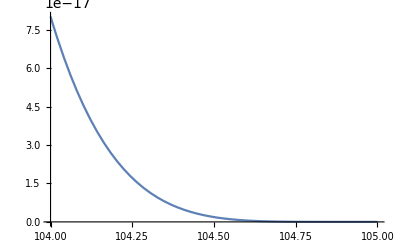

1.59558×10^-10

```mathematica
EconstAl=105.194
MconstAl=23273.122
a5Al=8.6434*10^-17
a6Al=1.16874*10^-17
a7Al=-1.87828*10^-19
a8Al=9.16327*10^-20
momResAl=0.2
EsigAl=92.29
f[x_]:=EconstAl-x-x^2/(2*MconstAl)
P[y_]:=a5Al*(f[y]^5)+a6Al*(f[y]^6)+a7Al*(f[y]^7)+a8Al*(f[y]^8)
Plot[P[z],{z,104.0,105}]
Integrate[P[z],{z,EsigAl-3*momResAl,EsigAl+3*momResAl}]
```

## Ti-48

104.394

44646.9

4.44278×10^-16

9.06648×10^-17

-4.26245×10^-18

8.193×10^-19

98.88

0.1

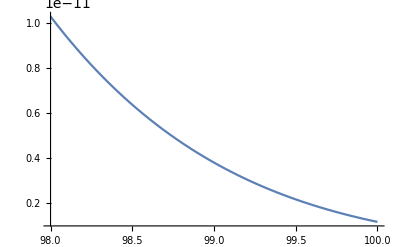

2.63396×10^-12

```mathematica
EconstTi=104.394
MconstTi=44646.861
a5Ti=4.44278*10^-16
a6Ti=9.06648*10^-17
a7Ti=-4.26245*10^-18
a8Ti=8.193*10^-19
EsigTi=98.88
momResTi=0.1
fTi[x_]:=EconstTi-x-x^2/(2*MconstTi)
PTi[y_]:=a5Ti*(fTi[y]^5)+a6Ti*(fTi[y]^6)+a7Ti*(fTi[y]^7)+a8Ti*(fTi[y]^8)
Plot[PTi[z],{z,98,100}]
Integrate[PTi[z],{z,EsigTi-3*momResTi,EsigTi+3*momResTi}]
```